```mathematica
dat = Import["/home/cjohns10/research/4BodySVDAtt2/adiabaticEnergies-100x100x100x50x5-HHHHEven.dat","Table"];
```

```mathematica
data = Transpose[Table[{dat[[i,1]],dat[[i,j]]},{i,1,98},{j,2,11}]];
```

```mathematica
{{{{{0.003707110173775119,346584.851469658},{0.01242375481435687,30909.9513033001},{0.02611346404772341,7038.09844881456},92,{9.97388653595228,-8.71392437594995},{9.98757624518564,-8.71362939872038},{9.99629288982623,-8.71344307108198}},{1},196,{1},{1}}}, {{{, , , , }}}}
```

{{0.00741422,173321.,433216.,433216.,808620.,808620.,808620.,1.29953×10^6,1.29953×10^6,1.29953×10^6,1.29953×10^6},{0.0248475,15481.4,38621.3,38621.5,72045.8,72045.9,72045.9,115755.,115755.,115755.,115755.},{0.0522269,3542.44,8780.06,8780.32,16345.6,16345.8,16345.9,26239.1,26239.1,26239.3,26239.3},{0.0895231,1233.86,3016.36,3016.8,5591.23,5591.6,5591.67,8958.46,8958.5,8958.89,8958.89},{0.136698,549.082,1313.43,1314.1,2417.73,2418.29,2418.41,3861.95,3862.02,3862.6,3862.61},{0.193706,286.589,667.071,668.014,1216.99,1217.78,1217.94,1936.31,1936.39,1937.22,1937.23},{0.260488,166.22,376.411,377.661,680.456,681.509,681.723,1078.32,1078.42,1079.54,1079.55},{0.336979,102.845,228.207,229.793,409.836,411.17,411.445,647.694,647.805,649.234,649.243},{0.423103,65.5532,144.817,146.753,259.975,261.603,261.945,410.988,411.098,412.876,412.878},{0.518773,41.5789,94.0323,96.3228,170.582,172.504,172.915,271.183,271.27,273.416,273.423},{0.623893,25.1016,61.0922,63.7252,113.978,116.181,116.659,183.702,183.74,186.264,186.284},{0.738361,13.2407,38.6643,41.6139,76.4031,78.8584,79.3949,126.323,126.365,129.229,129.265},{0.86206,4.45777,22.846,26.0736,50.5452,53.2056,53.785,87.2275,87.3874,90.5055,90.5616},{0.994869,-2.13325,11.4245,14.8832,32.2859,35.0867,35.6862,59.8236,60.1417,63.4501,63.5297},{1.13665,-7.08447,3.067,6.70656,19.1796,22.0395,22.6307,40.1921,40.7091,44.1269,44.2359},{1.28727,-10.7675,-3.07699,0.695219,9.69916,12.524,13.0767,25.9101,26.6621,30.0965,30.2437},{1.44658,-13.4505,-7.57919,-3.71717,2.84334,5.53286,6.02137,15.417,16.4296,19.7836,19.9814},{1.61441,-15.3379,-10.8403,-6.92601,-2.0763,0.382017,0.792557,7.67047,8.95127,12.1365,12.4002},{1.7906,-16.5915,-13.1494,-9.21861,-5.55506,-3.4074,-3.07042,1.95083,3.4843,6.43433,6.78025},{1.97497,-17.3427,-14.7199,-10.8108,-7.96309,-6.17796,-5.8897,-2.25257,-0.505864,2.17378,2.6169},{2.16735,-17.6984,-15.7128,-11.8686,-9.58471,-8.17858,-7.89673,-5.3108,-3.40771,-1.00307,-0.450939},{2.36753,-17.746,-16.2526,-12.5213,-10.6412,-9.59226,-9.26351,-7.49873,-5.5026,-3.35596,-2.68789},{2.57532,-17.5562,-16.4384,-12.8697,-11.3026,-10.5551,-10.1241,-9.02314,-6.99358,-5.07737,-4.29392},{2.79051,-17.1857,-16.3505,-12.9914,-11.6895,-11.1695,-10.594,-10.0415,-8.02866,-6.31229,-5.42467},{3.01288,-16.6805,-16.0546,-12.946,-11.8756,-11.5143,-10.7812,-10.6751,-8.71828,-7.17162,-6.20351},{3.24223,-16.0773,-15.6045,-12.7784,-11.9047,-11.6513,-11.0176,-10.7806,-9.14694,-7.74146,-6.72821},{3.4783,-15.4065,-15.0443,-12.5233,-11.8097,-11.63,-11.1424,-10.664,-9.38034,-8.08918,-7.0746},{3.72088,-14.6929,-14.4098,-12.2075,-11.6197,-11.4908,-11.1071,-10.4809,-9.47002,-8.26757,-7.29878},{3.96972,-13.9577,-13.7302,-11.8526,-11.3607,-11.2671,-10.9571,-10.2631,-9.45644,-8.31806,-7.43924},{4.22457,-13.2187,-13.0292,-11.4769,-11.0557,-10.9866,-10.7288,-10.0305,-9.37118,-8.27366,-7.51982},{4.48518,-12.4919,-12.3265,-11.0962,-10.7248,-10.6729,-10.4512,-9.79381,-9.23844,-8.16126,-7.55387},{4.75128,-11.7923,-11.6388,-10.7243,-10.3852,-10.3455,-10.1482,-9.55743,-9.07578,-8.00322,-7.54843},{5.02262,-11.136,-10.9813,-10.3738,-10.0511,-10.0213,-9.83927,-9.32024,-8.89443,-7.81816,-7.5075},{5.29891,-10.5434,-10.3701,-10.0549,-9.7323,-9.71436,-9.54027,-9.07501,-8.69883,-7.62117,-7.43414},{5.5799,-10.0431,-9.82615,-9.7756,-9.43585,-9.43256,-9.2639,-8.80659,-8.48513,-7.42405,-7.33207},{5.86529,-9.66196,-9.53983,-9.37945,-9.19336,-9.15182,-9.01926,-8.49604,-8.24024,-7.23529,-7.20687},{6.1548,-9.39641,-9.34755,-9.06015,-8.99036,-8.89418,-8.81138,-8.14305,-7.95072,-7.06656,-7.06021},{6.44814,-9.21345,-9.19508,-8.85072,-8.82611,-8.68031,-8.6411,-7.77743,-7.62624,-6.92093,-6.90138},{6.74502,-9.08329,-9.07658,-8.70562,-8.69673,-8.52165,-8.50572,-7.43351,-7.30015,-6.77979,-6.7597},{7.04515,-8.98804,-8.98563,-8.5999,-8.59665,-8.40647,-8.40039,-7.13354,-7.00357,-6.65111,-6.63542},{7.34823,-8.91716,-8.9163,-8.52127,-8.52009,-8.32179,-8.31953,-6.88766,-6.75417,-6.53976,-6.52848},{7.65395,-8.86391,-8.86361,-8.46226,-8.46183,-8.25875,-8.25792,-6.69585,-6.55733,-6.44733,-6.438},{7.962,-8.82368,-8.82358,-8.41775,-8.41759,-8.21142,-8.21112,-6.55075,-6.41132,-6.37294,-6.35999},{8.27209,-8.79318,-8.79315,-8.38403,-8.38398,-8.17567,-8.17556,-6.44209,-6.32189,-6.31426,-6.27761},{8.5839,-8.76997,-8.76996,-8.35841,-8.35839,-8.14854,-8.14851,-6.36039,-6.27079,-6.26847,-6.1974},{8.89712,-8.75224,-8.75224,-8.33885,-8.33885,-8.12786,-8.12785,-6.29839,-6.23383,-6.23287,-6.13373},{9.21144,-8.73864,-8.73864,-8.32386,-8.32385,-8.11201,-8.11201,-6.25094,-6.20559,-6.20516,-6.08443},{9.52655,-8.72816,-8.72816,-8.31229,-8.31229,-8.09979,-8.09979,-6.21436,-6.18367,-6.18348,-6.04627},{9.84213,-8.72002,-8.72002,-8.30332,-8.30332,-8.09031,-8.0903,-6.18603,-6.16646,-6.16638,-6.01665},{10.1579,-8.71366,-8.71366,-8.2963,-8.2963,-8.08288,-8.08288,-6.16401,-6.15278,-6.15276,-5.99359},{10.4734,-8.70864,-8.70864,-8.29076,-8.29076,-8.07702,-8.07702,-6.14684,-6.14178,-6.14178,-5.9756},{10.7886,-8.70464,-8.70464,-8.28634,-8.28634,-8.07235,-8.07235,-6.13348,-6.13283,-6.13274,-5.96151},{11.1029,-8.70142,-8.70142,-8.28278,-8.28278,-8.06858,-8.06858,-6.12546,-6.12544,-6.12282,-5.95046},{11.4161,-8.69881,-8.69881,-8.27987,-8.27987,-8.06551,-8.0655,-6.11927,-6.11926,-6.11452,-5.94174},{11.7279,-8.69665,-8.69665,-8.27748,-8.27748,-8.06296,-8.06296,-6.11403,-6.11402,-6.10795,-5.93485},{12.038,-8.69484,-8.69484,-8.27547,-8.27547,-8.06084,-8.06084,-6.10953,-6.10953,-6.10273,-5.92937},{12.3461,-8.69332,-8.69332,-8.27378,-8.27378,-8.05904,-8.05904,-6.10564,-6.10564,-6.09856,-5.92499},{12.6518,-8.69201,-8.69201,-8.27232,-8.27232,-8.0575,-8.05749,-6.10222,-6.10222,-6.09521,-5.92147},{12.9548,-8.69088,-8.69088,-8.27106,-8.27106,-8.05616,-8.05616,-6.0992,-6.0992,-6.0925,-5.91862},{13.255,-8.6899,-8.6899,-8.26996,-8.26996,-8.05499,-8.05499,-6.09651,-6.09651,-6.09029,-5.91629},{13.5519,-8.68902,-8.68902,-8.26899,-8.26899,-8.05395,-8.05395,-6.09409,-6.09409,-6.08848,-5.91438},{13.8452,-8.68824,-8.68824,-8.26812,-8.26812,-8.05303,-8.05303,-6.0919,-6.0919,-6.08697,-5.9128},{14.1347,-8.68754,-8.68754,-8.26734,-8.26733,-8.0522,-8.0522,-6.08991,-6.08991,-6.08572,-5.91148},{14.4201,-8.68691,-8.68691,-8.26663,-8.26663,-8.05145,-8.05145,-6.0881,-6.0881,-6.08466,-5.91036},{14.7011,-8.68633,-8.68633,-8.26599,-8.26598,-8.05077,-8.05077,-6.08643,-6.08643,-6.08377,-5.90941},{14.9774,-8.6858,-8.6858,-8.2654,-8.2654,-8.05014,-8.05014,-6.0849,-6.0849,-6.083,-5.9086},{15.2487,-8.68531,-8.68531,-8.26486,-8.26486,-8.04957,-8.04957,-6.08348,-6.08348,-6.08233,-5.9079},{15.5148,-8.68486,-8.68486,-8.26436,-8.26436,-8.04904,-8.04904,-6.08217,-6.08217,-6.08175,-5.90728},{15.7754,-8.68445,-8.68445,-8.2639,-8.2639,-8.04856,-8.04856,-6.08124,-6.08095,-6.08095,-5.90674},{16.0303,-8.68406,-8.68406,-8.26347,-8.26347,-8.04811,-8.04811,-6.08079,-6.07982,-6.07982,-5.90627},{16.2791,-8.6837,-8.6837,-8.26307,-8.26307,-8.04769,-8.04769,-6.08038,-6.07877,-6.07877,-5.90584},{16.5217,-8.68336,-8.68336,-8.2627,-8.2627,-8.0473,-8.0473,-6.08002,-6.0778,-6.0778,-5.90546},{16.7578,-8.68305,-8.68305,-8.26236,-8.26235,-8.04694,-8.04694,-6.0797,-6.07688,-6.07688,-5.90512},{16.9871,-8.68276,-8.68276,-8.26203,-8.26203,-8.0466,-8.0466,-6.0794,-6.07603,-6.07603,-5.90481},{17.2095,-8.68248,-8.68248,-8.26173,-8.26173,-8.04628,-8.04628,-6.07913,-6.07524,-6.07524,-5.90453},{17.4247,-8.68222,-8.68222,-8.26145,-8.26145,-8.04599,-8.04599,-6.07889,-6.0745,-6.0745,-5.90427},{17.6325,-8.68198,-8.68198,-8.26119,-8.26118,-8.04572,-8.04572,-6.07866,-6.07381,-6.07381,-5.90403},{17.8327,-8.68176,-8.68176,-8.26094,-8.26094,-8.04546,-8.04546,-6.07846,-6.07316,-6.07316,-5.90382},{18.025,-8.68154,-8.68154,-8.26071,-8.26071,-8.04522,-8.04522,-6.07827,-6.07256,-6.07256,-5.90362},{18.2094,-8.68135,-8.68135,-8.26049,-8.26049,-8.045,-8.045,-6.0781,-6.072,-6.072,-5.90344},{18.3856,-8.68116,-8.68116,-8.26029,-8.26029,-8.04479,-8.04479,-6.07794,-6.07147,-6.07147,-5.90328},{18.5534,-8.68099,-8.68099,-8.2601,-8.2601,-8.0446,-8.04459,-6.07779,-6.07099,-6.07099,-5.90313},{18.7127,-8.68083,-8.68083,-8.25992,-8.25992,-8.04442,-8.04441,-6.07766,-6.07054,-6.07054,-5.90299},{18.8633,-8.68068,-8.68068,-8.25976,-8.25976,-8.04425,-8.04425,-6.07753,-6.07012,-6.07012,-5.90286},{19.0051,-8.68054,-8.68054,-8.25961,-8.25961,-8.04409,-8.04409,-6.07742,-6.06973,-6.06973,-5.90274},{19.1379,-8.68041,-8.68041,-8.25947,-8.25946,-8.04395,-8.04395,-6.07732,-6.06938,-6.06938,-5.90264},{19.2616,-8.68029,-8.68029,-8.25934,-8.25933,-8.04382,-8.04382,-6.07722,-6.06906,-6.06905,-5.90254},{19.3761,-8.68018,-8.68018,-8.25922,-8.25922,-8.0437,-8.0437,-6.07714,-6.06876,-6.06876,-5.90245},{19.4812,-8.68009,-8.68009,-8.25911,-8.25911,-8.04359,-8.04359,-6.07706,-6.06849,-6.06849,-5.90238},{19.5769,-8.68,-8.68,-8.25901,-8.25901,-8.0435,-8.04349,-6.07699,-6.06825,-6.06825,-5.90231},{19.663,-8.67992,-8.67992,-8.25892,-8.25892,-8.04341,-8.04341,-6.07693,-6.06804,-6.06804,-5.90224},{19.7395,-8.67985,-8.67985,-8.25885,-8.25885,-8.04333,-8.04333,-6.07687,-6.06785,-6.06785,-5.90219},{19.8063,-8.67979,-8.67979,-8.25878,-8.25878,-8.04327,-8.04326,-6.07683,-6.06768,-6.06768,-5.90214},{19.8633,-8.67974,-8.67974,-8.25872,-8.25872,-8.04321,-8.04321,-6.07679,-6.06755,-6.06755,-5.9021},{19.9105,-8.67969,-8.67969,-8.25868,-8.25867,-8.04316,-8.04316,-6.07676,-6.06743,-6.06743,-5.90207},{19.9478,-8.67966,-8.67966,-8.25864,-8.25864,-8.04313,-8.04313,-6.07673,-6.06734,-6.06734,-5.90204},{19.9752,-8.67964,-8.67963,-8.25861,-8.25861,-8.0431,-8.0431,-6.07671,-6.06728,-6.06728,-5.90203},{19.9926,-8.67962,-8.67962,-8.25859,-8.25859,-8.04308,-8.04308,-6.0767,-6.06724,-6.06724,-5.90201}}

```mathematica
Evs = Flatten[Import["/home/cjohns10/research/4BodySVDAtt2/eigenValsNonSpys-HHLLEven.dat"]];
```

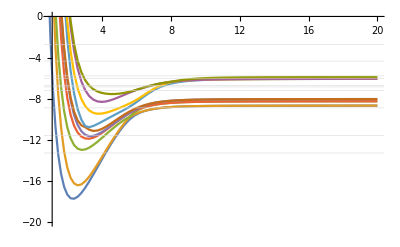

```mathematica
ListLinePlot[data, ImageSize->Full,PlotRange->{{1,20},{-20,-0}},GridLines->{None,Evs},GridLinesStyle->Thickness[0.001]]
```

```mathematica
Export["/home/cjohns10/research/4BodySVDAtt2/cplxAbsEsOnAd.jpg",%16,"JPEG"]
```

/home/cjohns10/research/4BodySVDAtt2/cplxAbsEsOnAd.jpg